# Analysis of Packing V3E05L1N01T1_1

Three Vertices, Five Edges, 1 Loop,Combinatorial Number 01, Face Pattern 1, Type 1

-Graphics-

This is a relatively cleaner packing, since the self tangency of the big circle gives rb=1/2.  To preserve all tangencies, we get the following two equations in terms of L and β.

Note that the center of circle 2 must be at (1/2, 1/2).   We also use perpendicular bisectors, as usual to solve for the center of circle 3.

Ok, now we have x and y in terms of L and θ but we also have one more piece of information which will let us solve for L in terms of β.  Law of Cosines!

```mathematica
Solve[√(1+L^2-√2 L (Cos[β]+Sin[β]))==(Sqrt[2]-1),L]
```

{{L→1/2 (-√2 (-Cos[β]-Sin[β])-√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2))},{L→1/2 (-√2 (-Cos[β]-Sin[β])+√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2))}}

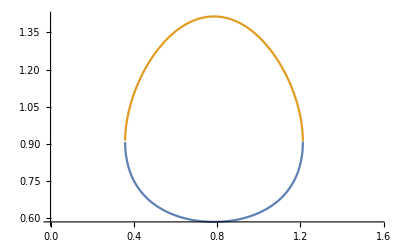

```mathematica
Plot[{1/2 (-√2 (-Cos[β]-Sin[β])-√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2)),1/2 (-√2 (-Cos[β]-Sin[β])+√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2))},{β,0,Pi/2}]
```

## Circle Centers and Radii

```mathematica
centers = Simplify[{{0,0},
{(1/2),
(1/2)},
{(1/2 (-√2 (-Cos[β]-Sin[β])+√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2)))*Cos[β+(Pi/4)]+(1/2),
(1/2 (-√2 (-Cos[β]-Sin[β])+√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2)))*Sin[β+(Pi/4)]-(1/2)}}]
```

{{0,0},{1/2,1/2},{1/2 (1+Cos[2 β]+Cos[β] √(5-4 √2+Sin[2 β])-Sin[β] √(5-4 √2+Sin[2 β])),1/2 (Sin[2 β]+(Cos[β]+Sin[β]) √(5-4 √2+Sin[2 β]))}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = Simplify[{
 {1,0},
{ (1/2 (-√2 (-Cos[β]-Sin[β])+√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2)))*Cos[β+(Pi/4)],(1/2 (-√2 (-Cos[β]-Sin[β])+√2 √(4-4 √2+Cos[β]^2+2 Cos[β] Sin[β]+Sin[β]^2)))*Sin[β+(Pi/4)]}}];
```

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,1,1,0},{1,2,0,0},{2,3,0,0},{2,1,1,0},{3,1,0,1},{3,1,1,1}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,Print["Edge ",i,": Length is ",FullSimplify[
EuclideanDistance[centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]],{β≥(Pi/3)-(Pi/4),β≤Pi/4}]]]
```

Edge 1: Length is 1

Edge 2: Length is 1/(√2)

Edge 3: Length is 1/2 √(Abs[(Cos[β]-Sin[β]) (Cos[β]+Sin[β]+√(5-4 √2+Sin[2 β]))]^2+Abs[1-Sin[2 β]-(Cos[β]+Sin[β]) √(5-4 √2+Sin[2 β])]^2)

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Edge 6: Length is 1/(√2)

```mathematica
Simplify[1/2 √(((Cos[β]-Sin[β]) (Cos[β]+Sin[β]+√(5-4 √2+Sin[2 β])))^2+(1-Sin[2 β]-(Cos[β]+Sin[β]) √(5-4 √2+Sin[2 β]))^2)]
```

√(3-2 √2)

```mathematica
N[√(3-2 √2)]
```

0.414214

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

The upper bound on β needs to be Pi/4 because we want to prevent any duplication.  Lower bound prevents tangencies being contained in a semi circle.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{b,Pi/4.1,"β"},ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4},AnimationRunning -> False (*middle value between b and β is where the slider starts*)
]
```

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{b,Pi/4.1,"β"},ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4},AnimationRunning -> False
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_2→1/2 (-1+Cos[2 β]+Sin[2 β]+2 Cos[β] √(5-4 √2+Sin[2 β])) ω_3,ω_4→-1/2 (1+Cos[2 β]-Sin[2 β]-2 Sin[β] √(5-4 √2+Sin[2 β])) ω_3,ω_5→-1/2 (1+Cos[2 β]-Sin[2 β]-2 Sin[β] √(5-4 √2+Sin[2 β])) ω_3,ω_6→1/2 (-1+Cos[2 β]+Sin[2 β]+2 Cos[β] √(5-4 √2+Sin[2 β])) ω_3}

Notice that stress ω_3 is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{α-> 5Pi/6,β-> 5Pi/6}]]
```

{{0.,0.},{0.,0.},{0.,0.}}

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.Subscript[ω, 3]->1]]
```

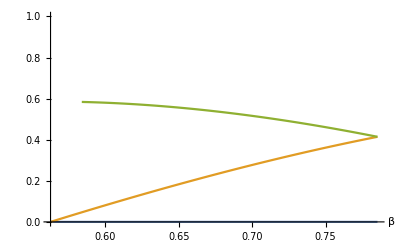

```mathematica
Plot[guts,{β,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4},RegionFunction->Function[{α,β},α>β],AxesLabel->Automatic]
```

So all stresses are positive. This is a locally maximally dense packing when *not* on the boundary!

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{β},Reals],ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))]<β<Pi/4}]
```

ArcCos[(Cos[π/4+β] (Conjugate[√(5-4 √2+Sin[2 β])]+Cos[β]+Sin[β]))/Abs[Cos[β]+Sin[β]+√(5-4 √2+Sin[2 β])]]

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{β},Reals],ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))]<β<Pi/4}]
```

Abs[Cos[β]+Sin[β]+√(5-4 √2+Sin[2 β])]/(√2)

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

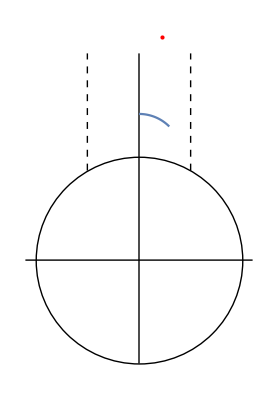

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{β,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4}],
(*Least dense globally maximally dense point*)
Graphics[{Red,Point[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]}/.{α->2.4907302,β->2.4907302}]}
]]
```

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{β},Reals],ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))]<β<Pi/4}]
```

((7-4 √2) π)/(√(8 Abs[Cos[β]+Sin[β]+√(5-4 √2+Sin[2 β])]^2+4 (Conjugate[√(5-4 √2+Sin[2 β])]+Cos[β]+Sin[β])^2 (-1+Sin[2 β])))

Plot the density over the parameter space

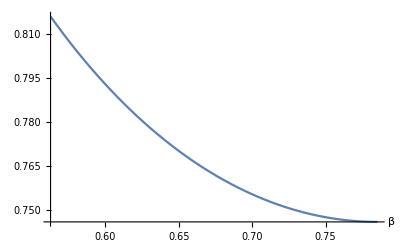

```mathematica
Plot[torusDensity,{β,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4},AxesLabel->Automatic]
```

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{β,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4},ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

-Graphics-

Now find the minimum and maximum density with in the region

```mathematica
NMinimize[{torusDensity,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))]< β && β < Pi/4 },{{β,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.7459299172987772276762524830236041020906,{β→0.7853981633974483096156608458198757210493}}

```mathematica
NMaximize[{torusDensity,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))]< β && β < Pi/4 },{{β,ArcTan[(1/Sqrt[2])/((1/Sqrt[2])+(Sqrt[2]-1))],Pi/4}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.815925236727520305218212098394421942729,{β→0.5626175364257851233560266796058198937188}}